```mathematica
Subscript[t, 0]=0;
Subscript[t, m]=25;
Subscript[p, 0]=0;
L=700;
Subscript[v, 0]=10;
Subscript[v, d]=25;
Subscript[v, m]=30;
res=Table[NMinimize[{1/3*Subscript[a, 1]^2(Subscript[t, 1]^3-Subscript[t, 0]^3)+Subscript[a, 1] Subscript[b, 1](Subscript[t, 1]^2-Subscript[t, 0]^2)+Subscript[b, 1]^2(Subscript[t, 1]-Subscript[t, 0])+1/3*Subscript[a, 2]^2(Subscript[t, m]^3-Subscript[t, 2]^3)+Subscript[a, 2] Subscript[b, 2](Subscript[t, m]^2-Subscript[t, 2]^2)+Subscript[b, 2]^2(Subscript[t, m]-Subscript[t, 2]),
1/2*Subscript[a, 1](Subscript[t, 1]^2-Subscript[t, 0]^2)+Subscript[b, 1](Subscript[t, 1]-Subscript[t, 0])+Subscript[v, 0]==Subscript[v, m]&&
1/2*Subscript[a, 2](Subscript[t, m]^2-Subscript[t, 2]^2)+Subscript[b, 2](Subscript[t, m]-Subscript[t, 2])+Subscript[v, m]-Subscript[v, d]==0&&
1/6*Subscript[a, 2](Subscript[t, m]^3-Subscript[t, 2]^3)+1/2*Subscript[b, 2](Subscript[t, m]^2-Subscript[t, 2]^2)+(Subscript[v, d]-1/2 Subscript[a, 2] Subscript[t, m]^2-Subscript[b, 2] Subscript[t, m])(Subscript[t, m]-Subscript[t, 2])+1/6*Subscript[a, 1](Subscript[t, 1]^3-Subscript[t, 0]^3)+1/2*Subscript[b, 1](Subscript[t, 1]^2-Subscript[t, 0]^2)+Subscript[v, 0](Subscript[t, 1]-Subscript[t, 0])+Subscript[p, 0]+Subscript[v, m](Subscript[t, 2]-Subscript[t, 1])==L&&
Subscript[t, m]≥Subscript[t, 2]≥Subscript[t, 1]≥Subscript[t, 0]&&Subscript[a, 1] Subscript[t, 0]+Subscript[b, 1]≥Subscript[a, 1] Subscript[t, 1]+Subscript[b, 1]≥0&&Subscript[v, d]≤Subscript[v, m]≤30&&0≥Subscript[a, 2] Subscript[t, 2]+Subscript[b, 2]≥Subscript[a, 2] Subscript[t, m]+Subscript[b, 2]},
{{Subscript[a, 1],-5,0},{Subscript[a, 2],-5,0},{Subscript[b, 1],5,20},{Subscript[b, 2],10,60},{Subscript[t, 1],0,Subscript[t, m]},{Subscript[t, 2],0,Subscript[t, m]},{Subscript[v, m],Subscript[v, d],30}},Method->{"NelderMead","ShrinkRatio"->0.95,"ContractRatio"->0.95,"ReflectRatio"->2,"RandomSeed"->2i}],{i,10}]
```

NMinimize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {10 + b_1\ t_1 + 1/2\ a_1\ t_1 2 - v_m == 0, 25 - b_2\ (25 - t_2) - 1/2\ a_2\ (625 - t_2 2) - v_m == 0, 600 - 10\ t_1 - 1/2\ b_1\ t_1 2 - 1/6\ a_1\ t_1 3 - (25 - 625\ a_2/2 - 25\ b_2)\ (25 - t_2) - 1/2\ b_2\ (625 - t_2 2) - 1/6\ a_2\ (15625 - t_2 3) - (-t_1 + t_2)\ v_m == 0, b_2 + a_2\ t_2 ≤ 0, a_1\ t_1 ≤ 0}.

NMinimize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {10 + b_1\ t_1 + 1/2\ a_1\ t_1 2 - v_m == 0, 25 - b_2\ (25 - t_2) - 1/2\ a_2\ (625 - t_2 2) - v_m == 0, 600 - 10\ t_1 - 1/2\ b_1\ t_1 2 - 1/6\ a_1\ t_1 3 - (25 - 625\ a_2/2 - 25\ b_2)\ (25 - t_2) - 1/2\ b_2\ (625 - t_2 2) - 1/6\ a_2\ (15625 - t_2 3) - (-t_1 + t_2)\ v_m == 0, b_2 + a_2\ t_2 ≤ 0}.

NMinimize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {10 + b_1\ t_1 + 1/2\ a_1\ t_1 2 - v_m == 0, 25 - b_2\ (25 - t_2) - 1/2\ a_2\ (625 - t_2 2) - v_m == 0, 600 - 10\ t_1 - 1/2\ b_1\ t_1 2 - 1/6\ a_1\ t_1 3 - (25 - 625\ a_2/2 - 25\ b_2)\ (25 - t_2) - 1/2\ b_2\ (625 - t_2 2) - 1/6\ a_2\ (15625 - t_2 3) - (-t_1 + t_2)\ v_m == 0, -b_1 - a_1\ t_1 ≤ 0, t_1 - t_2 ≤ 0}.

General::stop: Further output of NMinimize :: nosat will be suppressed during this calculation.

{{31.9202,{a_1→-0.150847,a_2→-1.25933,b_1→2.31784,b_2→28.9238,t_1→13.7106,t_2→22.9692,v_m→27.601}},{0.947635,{a_1→22.712,a_2→-1.99535,b_1→0.161634,b_2→50.3226,t_1→0.102536,t_2→24.3986,v_m→25.}},{29.28,{a_1→-0.1248,a_2→-0.1248,b_1→2.16,b_2→2.16,t_1→17.2988,t_2→17.3153,v_m→28.6923}},{0.00210413,{a_1→-15.1761,a_2→5.19043,b_1→55.8682,b_2→-67.2308,t_1→1.96593×10^-7,t_2→25.,v_m→26.6327}},{28.7006,{a_1→-0.121663,a_2→-0.68766,b_1→2.13381,b_2→17.186,t_1→25.039,t_2→25.,v_m→25.1455}},{32.3924,{a_1→-0.156678,a_2→-1.57797,b_1→2.35335,b_2→36.6386,t_1→13.5428,t_2→23.2196,v_m→27.5031}},{0.00631779,{a_1→2568.16,a_2→-3.2169×10^8,b_1→137546.,b_2→-1.30641×10^7,t_1→3.33939×10^-13,t_2→25.,v_m→25.}},{32.087,{a_1→-0.152872,a_2→-1.36605,b_1→2.3303,b_2→31.5039,t_1→13.6421,t_2→23.0634,v_m→27.565}},{29.28,{a_1→-0.1248,a_2→-0.1248,b_1→2.16,b_2→2.16,t_1→17.2996,t_2→17.3139,v_m→28.6923}},{0.995235,{a_1→34.6232,a_2→11.9513,b_1→-0.0831005,b_2→-380.425,t_1→0.136113,t_2→25.,v_m→25.}}}

```mathematica
res2 =Table[NMinimize[{1/3*Subscript[a, 1]^2(Subscript[t, 1]^3-Subscript[t, 0]^3)+Subscript[a, 1] Subscript[b, 1](Subscript[t, 1]^2-Subscript[t, 0]^2)+Subscript[b, 1]^2(Subscript[t, 1]-Subscript[t, 0])+1/3*Subscript[a, 2]^2(Subscript[t, m]^3-Subscript[t, 1]^3)+Subscript[a, 2] Subscript[b, 2](Subscript[t, m]^2-Subscript[t, 1]^2)+Subscript[b, 2]^2(Subscript[t, m]-Subscript[t, 1]),
1/2*Subscript[a, 1](Subscript[t, 1]^2-Subscript[t, 0]^2)+Subscript[b, 1](Subscript[t, 1]-Subscript[t, 0])+Subscript[v, 0]==Subscript[v, m]&&
1/2*Subscript[a, 2](Subscript[t, m]^2-Subscript[t, 1]^2)+Subscript[b, 2](Subscript[t, m]-Subscript[t, 1])+Subscript[v, m]==Subscript[v, d]&&
1/6*Subscript[a, 1](Subscript[t, 1]^3-Subscript[t, 0]^3)+1/2*Subscript[b, 1](Subscript[t, 1]^2-Subscript[t, 0]^2)+Subscript[v, 0](Subscript[t, 1]-Subscript[t, 0])+Subscript[p, 0]==Subscript[p, 1]&&
1/6*Subscript[a, 2](Subscript[t, m]^3-Subscript[t, 1]^3)+1/2*Subscript[b, 2](Subscript[t, m]^2-Subscript[t, 1]^2)+Subscript[v, m](Subscript[t, m]-Subscript[t, 1])+Subscript[p, 1]==L&&
Subscript[t, 1]≥Subscript[t, 0]&&Subscript[t, m]≥Subscript[t, 1]&&
Subscript[a, 1] Subscript[t, 0]+Subscript[b, 1]≥Subscript[a, 1] Subscript[t, 1]+Subscript[b, 1]≥0&&Subscript[a, 1]≤0&&
0≥Subscript[a, 2] Subscript[t, 1]+Subscript[b, 2]≥Subscript[a, 2] Subscript[t, m]+Subscript[b, 2]&&L≥Subscript[p, 1]≥Subscript[p, 0]&&Subscript[v, m]≤30},{{Subscript[a, 1],-1,0},{Subscript[b, 1],1,5},{Subscript[a, 2],-1,0},{Subscript[b, 2],-5,-1},{Subscript[t, 1],0,Subscript[t, m]},{Subscript[p, 1],0,L},{Subscript[v, m],0,30}},
Method->{"NelderMead","ShrinkRatio"->0.90,"ContractRatio"->0.95,"ReflectRatio"->2,"RandomSeed"->i}],{i,5}]
```

0

25

0

600

10

25

NMinimize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {p_1 - 10\ t_1 - 1/2\ b_1\ t_1 2 - 1/6\ a_1 2\ t_1 3 == 0, 10 + b_1\ t_1 + 1/2\ a_1\ t_1 2 - v_m == 0, 25 - b_2\ (25 - t_1) - 1/2\ a_2\ (625 - t_1 2) - v_m == 0, 600 - p_1 - 1/2\ b_2\ (625 - t_1 2) - 1/6\ a_2 2\ (15625 - t_1 3) - (25 - t_1)\ v_m == 0, -b_1 - a_1\ t_1 ≤ 0}.

{{11.39,{a_1→-0.0248983,b_1→0.978816,a_2→-0.038329,b_2→0.820876,t_1→21.4011,p_1→439.176,v_m→25.2459}},{32.0572,{a_1→-0.14521,b_1→2.58156,a_2→-0.00270911,b_2→0.0211451,t_1→7.58256,p_1→151.571,v_m→25.4004}},{11.0811,{a_1→-0.0399629,b_1→1.0996,a_2→-0.233205,b_2→5.82666,t_1→24.9852,p_1→597.22,v_m→25.}},{1151.13,{a_1→0.,b_1→-0.885098,a_2→-13.0021,b_2→4.71828,t_1→24.989,p_1→15.8277,v_m→28.0145}},{10.7536,{a_1→-0.0363549,b_1→1.05566,a_2→-0.152063,b_2→3.77325,t_1→24.8137,p_1→576.498,v_m→25.0026}}}

```mathematica
L=600;
Subscript[t, m]=25;
res3 =N[Solve[1/6 Subscript[t, m]^3 a+1/2 Subscript[t, m]^2 b+Subscript[v, 0] Subscript[t, m]==L && 1/2 Subscript[t, m]^2 a+Subscript[t, m] b+Subscript[v, 0]==Subscript[v, d],{a,b},Reals]]
```

{{a→-0.1248,b→2.16}}

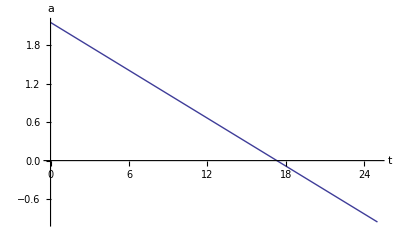

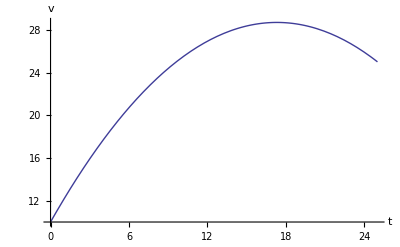

600.

14.64

```mathematica
u[t_]:=a t+b/.res3[[1]]
v[t_]:=1/2a t^2+b t+Subscript[v, 0]/.res3[[1]]
Plot[u[t],{t,0,Subscript[t, m]},PlotRange->All,AxesLabel->{t,a}]
Plot[v[t],{t,0,Subscript[t, m]},PlotRange->All,AxesLabel->{t,v}]
N[Integrate[v[t],{t,0,Subscript[t, m]}]]
N[Integrate[1/2(u[t])^2,{t,0,Subscript[t, m]}]]
```

```mathematica
Abs[1/2*Subscript[a, 1](Subscript[t, 1]^2-Subscript[t, 0]^2)+Subscript[b, 1](Subscript[t, 1]-Subscript[t, 0])+Subscript[v, 0]-Subscript[v, m]]≤10^-3&&
Abs[1/2*Subscript[a, 2](Subscript[t, m]^2-Subscript[t, 2]^2)+Subscript[b, 2](Subscript[t, m]-Subscript[t, 2])+Subscript[v, m]-Subscript[v, d]]≤10^-3&&
Abs[1/6*Subscript[a, 2](Subscript[t, m]^3-Subscript[t, 2]^3)+1/2*Subscript[b, 2](Subscript[t, m]^2-Subscript[t, 2]^2)+(Subscript[v, d]-1/2 Subscript[a, 2] Subscript[t, m]^2-Subscript[b, 2] Subscript[t, m])(Subscript[t, m]-Subscript[t, 2])+1/6*Subscript[a, 1](Subscript[t, 1]^3-Subscript[t, 0]^3)+1/2*Subscript[b, 1](Subscript[t, 1]^2-Subscript[t, 0]^2)+Subscript[v, 0](Subscript[t, 1]-Subscript[t, 0])+Subscript[p, 0]+Subscript[v, m](Subscript[t, 2]-Subscript[t, 1])-L]≤10^-3/.res[[3]][[2]]
```

True

{a_1→-0.899999,a_2→-0.899998,b_1→6.,b_2→19.4999,t_1→6.66314,t_2→21.67,v_m→30.}

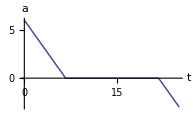

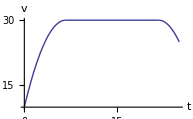

700.

45.

```mathematica
subs=res[[3]][[2]]
ac1={Subscript[a, 1] t+Subscript[b, 1]/.subs,0≤t<Subscript[t, 1]/.subs};
ac2={0,Subscript[t, 1]≤t<Subscript[t, 2]/.subs};
ac3={Subscript[a, 2] t+Subscript[b, 2]/.subs,Subscript[t, 2]≤t≤Subscript[t, m]/.subs};
u[t_]:=Piecewise[{ac1,ac2,ac3}]
vc1={1/2 Subscript[a, 1] t^2+Subscript[b, 1] t+Subscript[v, 0]/.subs,0≤t<Subscript[t, 1]/.subs};
vc2={Subscript[v, m]/.subs,Subscript[t, 1]≤t<Subscript[t, 2]/.subs};
vc3={1/2 Subscript[a, 2] t^2+Subscript[b, 2] t+(Subscript[v, d]-1/2 Subscript[a, 2] Subscript[t, m]^2-Subscript[b, 2] Subscript[t, m])/.subs,Subscript[t, 2]≤t≤Subscript[t, m]/.subs};
v[t_]:=Piecewise[{vc1,vc2,vc3}]
Plot[u[t],{t,0,Subscript[t, m]},PlotRange->All,AxesLabel->{t,a}]
Plot[v[t],{t,0,Subscript[t, m]},PlotRange->All,AxesLabel->{t,v}]
N[Integrate[v[t],{t,0,Subscript[t, m]}]]
N[Integrate[1/2(u[t])^2,{t,0,Subscript[t, m]}]]
```

```mathematica
(*Subscript[v, 0]=10;
Subscript[v, d]=25;
L=700;
a=.;
b=.;
Subscript[t, m]=25;
Subscript[v, m]=30;*)
Subscript[v, 0]=10;
Subscript[v, d]=25;
L=720;
Subscript[t, m]=30;
Subscript[v, m]=30;
res4=N[Solve[1/2 a t^2+b t+Subscript[v, 0]==Subscript[v, d]&&
1/6 a t^3+1/2 b t^2+Subscript[v, 0] t==L-(Subscript[t, m]-t)Subscript[v, m]&&
-b^2/(2a)+Subscript[v, 0]==Subscript[v, m],{a,b,t}]]
(2a t+b)/.res4
```

{{a→-0.0420096,b→1.2963,t→15.4286},{a→-0.0694444,b→1.66667,t→36.}}

{0.,-3.33333}

```mathematica
Subscript[t, 0]=0;
Subscript[t, m]=25;
Subscript[p, 0]=0;
L=600;
Subscript[v, 0]=10;
Subscript[v, m]=30;
Subscript[v, d]=25;
Subscript[u, max]=20;
Subscript[u, min]=-20;
cl=100;
res=Table[NMinimize[{
Subscript[u, 1] Subscript[t, 1]+1/3 Subscript[a, 1]^2(Subscript[t, 2]^3-Subscript[t, 1]^3)+Subscript[a, 1] Subscript[b, 1](Subscript[t, 2]^2-Subscript[t, 1]^2)+Subscript[b, 1]^2(Subscript[t, 2]-Subscript[t, 1])+1/3 Subscript[a, 2]^2(Subscript[t, 4]^3-Subscript[t, 3]^3)+Subscript[a, 2] Subscript[b, 2](Subscript[t, 4]^2-Subscript[t, 3]^2)+Subscript[b, 2]^2(Subscript[t, 4]-Subscript[t, 3])+Subscript[u, 2](Subscript[t, m]-Subscript[t, 4]),
Subscript[u, 1] Subscript[t, 1]+Subscript[v, 0]==1/2 Subscript[a, 1] Subscript[t, 1]^2+Subscript[b, 1] Subscript[t, 1]+Subscript[c, 1]&&
Subscript[v, m]==1/2 Subscript[a, 1] Subscript[t, 2]^2+Subscript[b, 1] Subscript[t, 2]+Subscript[c, 1]&&
1/2 Subscript[a, 2] Subscript[t, 3]^2+Subscript[b, 2] Subscript[t, 3]+Subscript[c, 2]==Subscript[v, m]&&
1/2 Subscript[a, 2] Subscript[t, 4]^2+Subscript[b, 2] Subscript[t, 4]+Subscript[c, 2]==Subscript[u, 2] Subscript[t, 4]+(Subscript[v, d]-Subscript[u, 2] Subscript[t, m])&&
1/2 Subscript[u, 1] Subscript[t, 1]^2+Subscript[v, 0] Subscript[t, 1]==1/6 Subscript[a, 1] Subscript[t, 1]^3+1/2 Subscript[b, 1] Subscript[t, 1]^2+Subscript[c, 1] Subscript[t, 1]+Subscript[d, 1]&&
Subscript[v, m] Subscript[t, 2]==1/6 Subscript[a, 1] Subscript[t, 2]^3+1/2 Subscript[b, 1] Subscript[t, 2]^2+Subscript[c, 1] Subscript[t, 2]+Subscript[d, 1]&&
Subscript[v, m] Subscript[t, 3]==1/6 Subscript[a, 2] Subscript[t, 3]^3+1/2 Subscript[b, 2] Subscript[t, 3]^2+Subscript[c, 2] Subscript[t, 3]+Subscript[d, 2]&&
1/6 Subscript[a, 2] Subscript[t, 4]^3+1/2 Subscript[b, 2] Subscript[t, 4]^2+Subscript[c, 2] Subscript[t, 4]+Subscript[d, 2]==1/2 Subscript[u, 2] Subscript[t, 4]^2+(Subscript[v, d]-Subscript[u, 2] Subscript[t, m])Subscript[t, 4]+(L-1/2 Subscript[u, 2] Subscript[t, m]^2-(Subscript[v, d]-Subscript[u, 2] Subscript[t, m])Subscript[t, m])&&
0≤Subscript[t, 1]≤Subscript[t, 2]≤Subscript[t, 3]≤Subscript[t, 4]≤Subscript[t, m]&&
Subscript[u, max]≥Subscript[u, 1]≥Subscript[a, 1] Subscript[t, 1]+Subscript[b, 1]≥Subscript[a, 1] Subscript[t, 2]+Subscript[b, 1]≥0≥Subscript[a, 2] Subscript[t, 3]+Subscript[b, 2]≥Subscript[a, 2] Subscript[t, 4]+Subscript[b, 2]≥Subscript[u, 2]≥Subscript[u, min]&&
Abs[Subscript[a, 1]]≤cl/5&&Abs[Subscript[a, 2]]≤cl/5&&Abs[Subscript[b, 1]]≤cl&&Abs[Subscript[b, 2]]≤cl&&Abs[Subscript[c, 1]]≤cl&&Abs[Subscript[c, 1]]≤cl&&Abs[Subscript[d, 1]]≤cl&&Abs[Subscript[d, 2]]≤cl&&
},
{{Subscript[a, 1],-5,0},{Subscript[a, 2],-5,0},{Subscript[b, 1],5,20},{Subscript[b, 2],10,60},{Subscript[t, 1],0,Subscript[t, m]},{Subscript[t, 2],0,Subscript[t, m]},{Subscript[t, 3],0,Subscript[t, m]},{Subscript[t, 4],0,Subscript[t, m]},Subscript[c, 1],Subscript[c, 2],Subscript[d, 1],Subscript[d, 2],{Subscript[u, 1],0,12},{Subscript[u, 2],-12,0}},Method->{"RandomSearch"(*,"ShrinkRatio"->0.95,"ContractRatio"->0.95,"ReflectRatio"->2,"PerturbationScale"->3*),"RandomSeed"->5i}],{i,3}]
```

NMinimize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {30 - c_1 - b_1\ t_2 - 1/2\ a_1\ t_2 2 == 0, -d_1 + 30\ t_2 - c_1\ t_2 - 1/2\ b_1\ t_2 2 - 1/6\ a_1\ t_2 3 == 0, 30 - c_2 - b_2\ t_3 - 1/2\ a_2\ t_3 2 == 0, -d_2 + 30\ t_3 - c_2\ t_3 - 1/2\ b_2\ t_3 2 - 1/6\ a_2\ t_3 3 == 0, -10 + c_1 + b_1\ t_1 + 1/2\ a_1\ t_1 2 - t_1\ u_1 == 0, d_1 - 10\ t_1 + c_1\ t_1 + 1/2\ b_1\ t_1 2 + 1/6\ a_1\ t_1 3 - 1/2\ t_1 2\ u_1 == 0, -25 + c_2 + b_2\ t_4 + 1/2\ a_2\ t_4 2 + 25\ u_2 - t_4\ u_2 == 0, -600 + d_2 + c_2\ t_4 + 1/2\ b_2\ t_4 2 + 1/6\ a_2\ t_4 3 + 25\ (25 - 25\ u_2) - t_4\ (25 - 25\ u_2) + 625\ u_2/2 - 1/2\ t_4 2\ u_2 == 0, -a_1\ t_1 + a_1\ t_2 ≤ 0, -b_1 - a_1\ t_2 ≤ 0, -a_2\ t_3 + a_2\ t_4 ≤ 0, -b_2 - a_2\ t_4 + u_2 ≤ 0, t_2 - t_3 ≤ 0}.

General::stop: Further output of NMinimize :: nosat will be suppressed during this calculation.

{{47.3011,{a_1→0.0608736,a_2→0.0861408,b_1→-1.10659,b_2→-1.96591,t_1→1.20705,t_2→5.47149,t_3→5.13071,t_4→16.0269,c_1→35.5044,c_2→38.681,d_1→-15.2993,d_2→-20.6305,u_1→20.,u_2→0.750795}},{47.3054,{a_1→0.060816,a_2→0.0862067,b_1→-1.10597,b_2→-1.96704,t_1→1.20701,t_2→5.47284,t_3→5.13255,t_4→16.0261,c_1→35.5026,c_2→38.6891,d_1→-15.2977,d_2→-20.6583,u_1→20.,u_2→0.750852}},{47.3045,{a_1→0.0608267,a_2→0.0861924,b_1→-1.10609,b_2→-1.9668,t_1→1.20702,t_2→5.47255,t_3→5.13217,t_4→16.0263,c_1→35.503,c_2→38.6874,d_1→-15.298,d_2→-20.6525,u_1→20.,u_2→0.750842}}}

```mathematica
Subscript[t, m]=25;
L=720;
Subscript[v, 0]=10;
Subscript[v, d]=25;
Subscript[v, m]=30;
Subscript[u, m]=8;
res6 =N[Solve[
1/2 a Subscript[t, c]^2+Subscript[u, m] Subscript[t, c]+c==Subscript[v, d]&&
(-Subscript[u, m]^2)/(2a)+c==Subscript[v, m]&&
1/6 a Subscript[t, c]^3+1/2 Subscript[u, m] Subscript[t, c]^2+c Subscript[t, c]+1/2 Subscript[u, m] Subscript[t, a]^2+Subscript[v, 0] Subscript[t, a]+Subscript[v, m](Subscript[t, m]-Subscript[t, a]-Subscript[t, c])==L&&
Subscript[u, m] Subscript[t, a]+Subscript[v, 0]==c,
{a,c,Subscript[t, a],Subscript[t, c]},Reals]]
```

{{a→-1.51617,c→8.8942,t_a→-0.138224,t_c→2.70827},{a→-3.21692,c→20.0526,t_a→1.25657,t_c→4.24997}}

{a→-3.21692,c→20.0526,t_a→1.25657,t_c→4.24997}

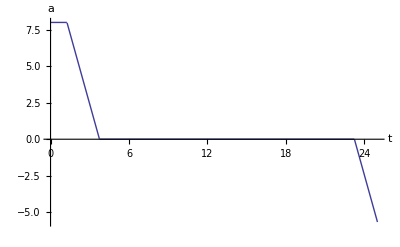

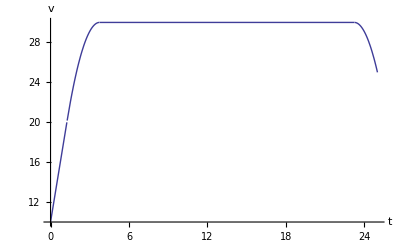

720.

76.1898

```mathematica
subs=res6[[2]]
ac0={Subscript[u, m],0≤t<Subscript[t, a]/.subs};
ac1={a(t-Subscript[t, a])+Subscript[u, m]/.subs,Subscript[t, a]≤t<Subscript[t, a]-Subscript[u, m]/a/.subs};
ac2={0,Subscript[t, a]-Subscript[u, m]/a≤t<Subscript[t, m]-Subscript[u, m]/a-Subscript[t, c]/.subs};
ac3={a (t-Subscript[t, m]+Subscript[u, m]/a+Subscript[t, c])/.subs,Subscript[t, m]-Subscript[u, m]/a-Subscript[t, c]≤t≤Subscript[t, m]/.subs};
u[t_]:=Piecewise[{ac0,ac1,ac2,ac3}]
vc0={Subscript[u, m] t+Subscript[v, 0],0≤t<Subscript[t, a]/.subs};
vc1={1/2 a t^2+(Subscript[u, m]-a Subscript[t, a])t+Subscript[v, 0]+1/2 a Subscript[t, a]^2/.subs,Subscript[t, a]≤t<Subscript[t, a]-Subscript[u, m]/a/.subs};
vc2={Subscript[v, m],Subscript[t, a]-Subscript[u, m]/a≤t<Subscript[t, m]-Subscript[u, m]/a-Subscript[t, c]/.subs};
tmp=(Subscript[t, m]-Subscript[u, m]/a-Subscript[t, c]/.subs);
vc3={1/2 a t^2-a tmp t+Subscript[v, m]+1/2 a tmp^2/.subs,Subscript[t, m]-Subscript[u, m]/a-Subscript[t, c]≤t≤Subscript[t, m]/.subs};
v[t_]:=Piecewise[{vc0,vc1,vc2,vc3}]
Plot[u[t],{t,0,Subscript[t, m]},PlotRange->All,AxesLabel->{t,a}]
Plot[v[t],{t,0,Subscript[t, m]},PlotRange->All,AxesLabel->{t,v}]
N[Integrate[v[t],{t,0,Subscript[t, m]}]]
N[Integrate[1/2(u[t])^2,{t,0,Subscript[t, m]}]]
```

```mathematica
Subscript[t, a]+Subscript[t, c]/.subs
```

5.50654

```mathematica
Subscript[t, 0]=0;
Subscript[t, m]=25;
Subscript[p, 0]=0;
L=720;
Subscript[v, 0]=10;
Subscript[v, d]=25;
Subscript[v, m]=30;
Subscript[u, m]=10;
Subscript[u, p]=-5;
res7 =N[Solve[
(-Subscript[u, m]^2)/(2a)+c==Subscript[v, m]&&
a Subscript[t, c]+Subscript[u, m]==Subscript[u, p]&&
1/2 a Subscript[t, c]^2+Subscript[u, m] Subscript[t, c]+c==Subscript[v, d]-Subscript[u, p] Subscript[t, e]&&
1/6 a Subscript[t, c]^3+1/2 Subscript[u, m] Subscript[t, c]^2+c Subscript[t, c]+1/2 Subscript[u, m] Subscript[t, a]^2+Subscript[v, 0] Subscript[t, a]+1/2 Subscript[u, p] Subscript[t, e]^2+(Subscript[v, d]-Subscript[u, p] Subscript[t, e])Subscript[t, e]+Subscript[v, m](Subscript[t, m]-Subscript[t, a]-Subscript[t, c]-Subscript[t, e])==L&&
Subscript[u, m] Subscript[t, a]+Subscript[v, 0]==c,
{a,c,Subscript[t, a],Subscript[t, c],Subscript[t, e]},Reals]]
```

{{a→-2.5,c→10.,t_a→0.,t_c→6.,t_e→0.},{a→2.5,c→50.,t_a→4.,t_c→-6.,t_e→2.}}

{a→-2.5,c→10.,t_a→0.,t_c→6.,t_e→0.}

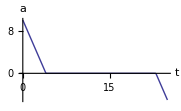

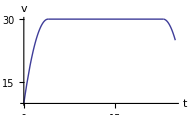

720.

75.

```mathematica
subs=res7[[1]]
Subscript[t, 1]=Subscript[t, a];
Subscript[t, 2]=Subscript[t, 1]-Subscript[u, m]/a;
Subscript[t, 3]=Subscript[t, 2]+Subscript[t, m]-Subscript[t, a]-Subscript[t, c]-Subscript[t, e];
Subscript[t, 4]=Subscript[t, m]-Subscript[t, e];
ac0={Subscript[u, m],0≤t<Subscript[t, 1]/.subs};
ac1={a(t-Subscript[t, 1])+Subscript[u, m]/.subs,Subscript[t, 1]≤t<Subscript[t, 2]/.subs};
ac2={0,Subscript[t, 2]≤t<Subscript[t, 3]/.subs};
ac3={a (t-Subscript[t, 3])/.subs,Subscript[t, 3]≤t≤Subscript[t, 4]/.subs};
ac4={Subscript[u, p],Subscript[t, 4]≤t≤Subscript[t, m]/.subs};
u[t_]:=Piecewise[{ac0,ac1,ac2,ac3,ac4}]
vc0={Subscript[u, m] t+Subscript[v, 0],0≤t<Subscript[t, 1]/.subs};
vc1={1/2 a t^2+(Subscript[u, m]-a Subscript[t, 1])t+Subscript[v, 0]+1/2 a Subscript[t, 1]^2/.subs,Subscript[t, 1]≤t<Subscript[t, 2]/.subs};
vc2={Subscript[v, m],Subscript[t, 2]≤t<Subscript[t, 3]/.subs};
vc3={1/2 a t^2-a Subscript[t, 3] t+Subscript[v, m]+1/2 a Subscript[t, 3]^2/.subs,Subscript[t, 3]≤t≤Subscript[t, 4]/.subs};
vc4={Subscript[u, p] t+Subscript[v, d]-Subscript[u, p] Subscript[t, m]/.subs,Subscript[t, 4]≤t≤Subscript[t, m]/.subs};
v[t_]:=Piecewise[{vc0,vc1,vc2,vc3,vc4}]
Plot[u[t],{t,0,Subscript[t, m]},PlotRange->All,AxesLabel->{t,a}]
Plot[v[t],{t,0,Subscript[t, m]},PlotRange->All,AxesLabel->{t,v}]
N[Integrate[v[t],{t,0,Subscript[t, m]}]]
N[Integrate[1/2(u[t])^2,{t,0,Subscript[t, m]}]]
```

```mathematica
Solve[um(t1-t0)==vm-v0&&
um(tm-t2)==vm-vd&&
1/2(vm+v0)(t1-t0)+vm(t2-t1)+1/2(vm+vd)(tm-t2)==LL,{tm,t1,t2}]
```

{{tm→-(-2 LL um-v0^2-vd^2-2 t0 um vm+2 v0 vm+2 vd vm-2 vm^2)/(2 um vm),t1→-(-t0 um+v0-vm)/um,t2→-(-2 LL um-v0^2-vd^2-2 t0 um vm+2 v0 vm)/(2 um vm)}}

```mathematica
tm=100.0;
v0=10.0;
vd=25.0;
L=720;
vm=5.0;
tc=.;
a=.;
b=.;
res8=N[Solve[
1/2*a*tc^2+b*tc+v0-vd==0&&
v0-b^2/(2*a)-vm==0&&
1/6*a*tc^3+1/2*b*tc^2+v0*tc-L+(tm-tc)*vm==0,{a,b,tc}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a→0.0281221,b→0.530303,tc→18.8571},{a→0.0464876,b→-0.681818,tc→44.}}

{a→0.0464876,b→-0.681818,tc→44.}

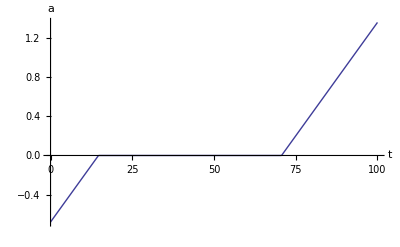

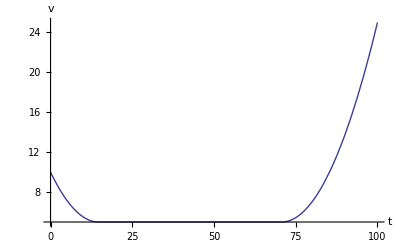

720.

10.2273

```mathematica
subs=res8[[2]]
Subscript[t, 1]=-b/a;
Subscript[t, 2]=Subscript[t, 1]+tm-tc;
ac0={a t+b/.subs,0≤t<Subscript[t, 1]/.subs};
ac1={0/.subs,Subscript[t, 1]≤t<Subscript[t, 2]/.subs};
ac2={a (t-Subscript[t, 2])/.subs,Subscript[t, 2]≤t<tm/.subs};
u[t_]:=Piecewise[{ac0,ac1,ac2}]
vc0={1/2 a t^2+b t+Subscript[v, 0]/.subs,0≤t<Subscript[t, 1]/.subs};
vc1={vm,Subscript[t, 1]≤t<Subscript[t, 2]/.subs};
vc2={1/2 a t^2-a Subscript[t, 2] t+vm+1/2 a Subscript[t, 2]^2/.subs,Subscript[t, 2]≤t<tm/.subs};
v[t_]:=Piecewise[{vc0,vc1,vc2}]
Plot[u[t],{t,0,tm},PlotRange->All,AxesLabel->{t,a}]
Plot[v[t],{t,0,tm},PlotRange->All,AxesLabel->{t,v}]
N[Integrate[v[t],{t,0,tm}]]
N[Integrate[1/2(u[t])^2,{t,0,tm}]]
```

```mathematica
2a tc+b/.res8[[1]]
```

1.59091

```mathematica
Subscript[t, 0]=0;
Subscript[t, m]=25;
Subscript[p, 0]=0;
L=700;
Subscript[v, 0]=10;
Subscript[v, d]=25;
```

Unset::norep: Assignment on Subscript for v_m not found.

```mathematica
res=Table[NMinimize[{1/3*Subscript[a, 1]^2(Subscript[t, 1]^3-Subscript[t, 0]^3)+Subscript[a, 1] Subscript[b, 1](Subscript[t, 1]^2-Subscript[t, 0]^2)+Subscript[b, 1]^2(Subscript[t, 1]-Subscript[t, 0])+1/3*Subscript[a, 2]^2(Subscript[t, m]^3-Subscript[t, 2]^3)+Subscript[a, 2] Subscript[b, 2](Subscript[t, m]^2-Subscript[t, 2]^2)+Subscript[b, 2]^2(Subscript[t, m]-Subscript[t, 2]),
1/2*Subscript[a, 1](Subscript[t, 1]^2-Subscript[t, 0]^2)+Subscript[b, 1](Subscript[t, 1]-Subscript[t, 0])+Subscript[v, 0]==Subscript[v, m]&&
1/2*Subscript[a, 2](Subscript[t, m]^2-Subscript[t, 2]^2)+Subscript[b, 2](Subscript[t, m]-Subscript[t, 2])+Subscript[v, m]-Subscript[v, d]==0&&
1/6*Subscript[a, 2](Subscript[t, m]^3-Subscript[t, 2]^3)+1/2*Subscript[b, 2](Subscript[t, m]^2-Subscript[t, 2]^2)+(Subscript[v, d]-1/2 Subscript[a, 2] Subscript[t, m]^2-Subscript[b, 2] Subscript[t, m])(Subscript[t, m]-Subscript[t, 2])+1/6*Subscript[a, 1](Subscript[t, 1]^3-Subscript[t, 0]^3)+1/2*Subscript[b, 1](Subscript[t, 1]^2-Subscript[t, 0]^2)+Subscript[v, 0](Subscript[t, 1]-Subscript[t, 0])+Subscript[p, 0]+Subscript[v, m](Subscript[t, 2]-Subscript[t, 1])==L&&
Subscript[t, m]≥Subscript[t, 2]≥Subscript[t, 1]≥Subscript[t, 0]&&Subscript[a, 1] Subscript[t, 0]+Subscript[b, 1]≥Subscript[a, 1] Subscript[t, 1]+Subscript[b, 1]≥0&&Subscript[v, d]≤Subscript[v, m]≤30&&0≥Subscript[a, 2] Subscript[t, 2]+Subscript[b, 2]≥Subscript[a, 2] Subscript[t, m]+Subscript[b, 2]},
{{Subscript[a, 1],-5,0},{Subscript[a, 2],-5,0},{Subscript[b, 1],5,20},{Subscript[b, 2],10,60},{Subscript[t, 1],0,Subscript[t, m]},{Subscript[t, 2],0,Subscript[t, m]},{Subscript[v, m],Subscript[v, d],30}},Method->{"NelderMead","ShrinkRatio"->0.95,"ContractRatio"->0.95,"ReflectRatio"->2,"RandomSeed"->2i}],{i,10}]
```

NMinimize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {10 + b_1\ t_1 + 1/2\ a_1\ t_1 2 - v_m == 0, 25 - b_2\ (25 - t_2) - 1/2\ a_2\ (625 - t_2 2) - v_m == 0, 700 - 10\ t_1 - 1/2\ b_1\ t_1 2 - 1/6\ a_1\ t_1 3 - (25 - 625\ a_2/2 - 25\ b_2)\ (25 - t_2) - 1/2\ b_2\ (625 - t_2 2) - 1/6\ a_2\ (15625 - t_2 3) - (-t_1 + t_2)\ v_m == 0, b_2 + a_2\ t_2 ≤ 0, a_1\ t_1 ≤ 0, 25\ a_2 - a_2\ t_2 ≤ 0}.

{{90.,{a_1→-0.9,a_2→-0.9,b_1→6.,b_2→19.5,t_1→6.66639,t_2→21.6675,v_m→30.}},{510.122,{a_1→-6.22911,a_2→-51.8806,b_1→16.6683,b_2→1216.05,t_1→1.57173,t_2→24.9561,v_m→28.5041}},{90.,{a_1→-0.899999,a_2→-0.899998,b_1→6.,b_2→19.4999,t_1→6.66314,t_2→21.67,v_m→30.}},{90.4282,{a_1→-0.926215,a_2→-0.484871,b_1→6.09571,b_2→9.71891,t_1→6.22471,t_2→22.0284,v_m→30.}},{2108.67,{a_1→-3.19281,a_2→-0.82022,b_1→115.579,b_2→12.7663,t_1→0.156782,t_2→24.5931,v_m→28.0816}},{90.2578,{a_1→-0.869418,a_2→-1.21736,b_1→5.89715,b_2→26.9451,t_1→6.78285,t_2→22.1459,v_m→29.9998}},{1442.69,{a_1→-7.31254,a_2→-31.6065,b_1→78.943,b_2→776.161,t_1→0.231792,t_2→24.557,v_m→28.1019}},{90.,{a_1→-0.899999,a_2→-0.899998,b_1→6.,b_2→19.5,t_1→6.66248,t_2→21.6704,v_m→30.}},{90.,{a_1→-0.899999,a_2→-0.899996,b_1→6.,b_2→19.4999,t_1→6.66221,t_2→21.6712,v_m→30.}},{27.9248,{a_1→29.2397,a_2→4.45632,b_1→6.21342,b_2→-105.163,t_1→0.248771,t_2→24.9273,v_m→28.0866}}}